```mathematica
nmax = 10; α = 0.8; Γ=(1.84 10^6);
Matrix Elements
Mat = {{89.73189120000002,0.2000032085333334,0.00011002339486927706,2.509395207314289*^-8,3.0695515946391326*^-12,2.3250055277701026*^-16,1.1940374668425611*^-20,4.424592855848029*^-25,1.2377275732321855*^-29,2.7050153862222876*^-34},{0.20000320853333353,80.3993918426986,0.42176986859201127,0.0004202719902583808,1.5132663420174065*^-7,2.6830212412543234*^-11,2.778615863887534*^-15,1.8700047808518214*^-19,8.792254592656171*^-24,3.042512759827579*^-28},{0.00011002339486928319,0.4217698685920112,71.92462014254228,0.7025623820717465,0.0011147200944999723,5.840071353620498*^-7,1.4186359814798123*^-10,1.927640601808704*^-14,1.6473445778916955*^-18,9.586405027278855*^-23},{2.5093952073193054*^-8,0.00042027199025840436,0.7025623820717465,64.2357646370139,1.0282778686958816,0.0023946294240447677,1.725493862251961*^-6,5.510751522545706*^-10,9.520128853790232*^-14,1.0077623425949352*^-17},{3.0695515914077746*^-12,1.513266342020434*^-7,0.0011147200945000376,1.028277868695882,57.26664226072516,1.3865964393346133,0.004480598620139658,4.261365742966132*^-6,1.7338927736595383*^-9,3.71489168840939*^-13},{2.32500784847032*^-16,2.6830212384298715*^-11,5.840071353632175*^-7,0.002394629424044907,1.3865964393346124,50.95628622259219,1.7668107702829745,0.007603375809215791,9.249172745226676*^-6,4.677056482052234*^-9},{1.1939307864547287*^-20,2.7786186373581163*^-15,1.4186359799863958*^-10,1.7254938622554135*^-6,0.004480598620139917,1.7668107702829756,45.24856183222715,2.159669298304147,0.011996076290873323,0.000018207670537881466},{4.348768556079334*^-25,1.8698377066679602*^-19,1.9276425258798086*^-14,5.510751516744465*^-10,4.2613657429746546*^-6,0.00760337580921622,2.1596692983041494,40.09180852805582,2.5572320857578186,0.017887660163669276},{5.197197497300727*^-29,8.641581622374825*^-24,1.6471973971177688*^-18,9.520138356290255*^-14,1.7338927718342476*^-9,9.249172745245187*^-6,0.011996076290874014,2.5572320857578226,35.438506460400546,2.9527384644418437},{9.773198716377846*^-27,1.277546048326997*^-27,9.42212269166648*^-23,1.0076723048192896*^-17,3.7148953964220513*^-13,4.6770564771286365*^-9,0.000018207670537917916,0.017887660163670306,2.9527384644418477,31.24496607813421}};
```

```mathematica
Matd = Mat.Inverse[IdentityMatrix[nmax]-(1-α)*Mat]
```

{{-5.29505,0.00078267,-4.44795×10^-6,4.73413×10^-8,-8.39371×10^-10,2.29502×10^-11,-9.18814×10^-13,5.19706×10^-14,-4.05187×10^-15,4.21075×10^-16},{0.00078267,-5.33158,0.00208991,-0.0000224417,3.98187×10^-7,-1.08879×10^-8,4.359×10^-10,-2.46557×10^-11,1.92227×10^-12,-1.99765×10^-13},{-4.44795×10^-6,0.00208991,-5.37361,0.00443259,-0.0000792947,2.16961×10^-6,-8.68651×10^-8,4.91334×10^-9,-3.83067×10^-10,3.98088×10^-11},{4.73413×10^-8,-0.0000224417,0.00443259,-5.42224,0.00831299,-0.000229172,9.18058×10^-6,-5.19301×10^-7,4.04872×10^-8,-4.20748×10^-9},{-8.39371×10^-10,3.98187×10^-7,-0.0000792947,0.00831299,-5.47886,0.0144703,-0.000583674,0.0000330317,-2.57539×10^-6,2.67639×10^-7},{2.29502×10^-11,-1.08879×10^-8,2.16961×10^-6,-0.000229172,0.0144703,-5.54535,0.0240114,-0.00136735,0.000106653,-0.0000110838},{-9.18814×10^-13,4.359×10^-10,-8.68651×10^-8,9.18058×10^-6,-0.000583674,0.0240114,-5.62427,0.0386349,-0.00303038,0.000315039},{5.19706×10^-14,-2.46557×10^-11,4.91334×10^-9,-5.19301×10^-7,0.0000330317,-0.00136735,0.0386349,-5.71924,0.0610287,-0.00637597},{-4.05187×10^-15,1.92227×10^-12,-3.83067×10^-10,4.04872×10^-8,-2.57539×10^-6,0.000106653,-0.00303038,0.0610287,-5.83557,0.0939657},{4.21075×10^-16,-1.99765×10^-13,3.98088×10^-11,-4.20748×10^-9,2.67639×10^-7,-0.0000110838,0.000315039,-0.00637597,0.0939657,-5.96313}}

### Effective Scattering rate

```mathematica
αeff[n_] := α
Ω[n_] := Ωfree *Sqrt[n];
Ωfree = 2 3.14159 * 30.6 10^3;
ωR = 3 10^8*2 3.14159 / (455*10^-9);
δ2 = 0;δ12 =0;
δ1 = 0
```

0

```mathematica
Γeff[n_,δ1_] := (ωR^2 Ω[n]^2)/(2*Ω[n]^2(Γ^2+Ω[n]^2+(1-αeff[n])(2 *δ1^2+ωR^2)+4δ12(δ2-2 αeff[n] *δ1))+αeff[n]*(4*Γ^2*δ1^2+(ωR^2+4 *δ1 *δ12)^2))
```

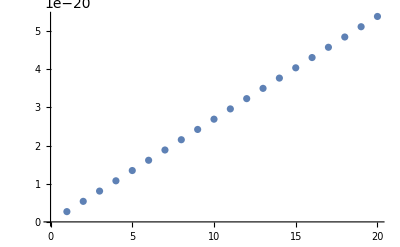

```mathematica
ListPlot[Table[{n,Γeff[n, 1]},{n,1,20}]]
```

```mathematica
Γeff[1,1]
```

2.69236×10^-21

```mathematica
Heating rates
```

```mathematica
Γheat = 1 2 * Pi * 10^3;
```

Rate Equation

```mathematica
Γeff[n_] := 2 * Pi * 10^3*n
```

```mathematica
Pm[t_] := {P1[t],P2[t],P3[t],P4[t],P5[t],P6[t],P7[t],P8[t],P9[t],P10[t]}
```

```mathematica
Pm'[t]
```

{P1'[t],P2'[t],P3'[t],P4'[t],P5'[t],P6'[t],P7'[t],P8'[t],P9'[t],P10'[t]}

```mathematica
Clear[Matd, Γeff, Γheat, α]
```

```mathematica
R = Table[+α(Γeff[n]*Matd[[n,nt-1]]+Γheat*Matd[[n,nt]]), {n,1,nmax},{nt,1,nmax}] ;
For[i=2,i≤ nmax,i++,R[[i,i]] = R[[i,i]] -(Γeff[i]+ Γheat)]
For[i=1,i≤ nmax,i++,R[[i,1]] = α Γheat*Matd[[1,i]]]
R[[1,1]] =-(Γeff[1]+ Γheat) -  α Γheat*Matd[[1,1]];
```

```mathematica
R //MatrixForm //N
```

(14049.5 | -26611.9 | 3.91177 | -0.0221199 | 0.000233744 | -4.10378×10^-6 | 1.10742×10^-7 | -4.35723×10^-9 | 2.40866×10^-10 | -1.82503×10^-11
3.93413 | -45641.1 | -53588.4 | 20.8973 | -0.223607 | 0.00394828 | -0.000107266 | 4.25822×10^-6 | -2.38204×10^-7 | 1.83207×10^-8
-0.0223578 | 10.438 | -52112. | -81009.9 | 66.4433 | -1.18483 | 0.0322803 | -0.0012852 | 0.0000721659 | -5.57641×10^-6
0.000237963 | -0.111852 | 21.8294 | -58582. | -108979. | 165.991 | -4.56162 | 0.181976 | -0.0102376 | 0.000792894
-4.21914×10^-6 | 0.00198041 | -0.388571 | 39.7927 | -65030. | -137626. | 360.745 | -14.5033 | 0.817231 | -0.0633814
1.1536×10^-7 | -0.0000540363 | 0.0105773 | -1.08651 | 65.8241 | -71419.9 | -167123. | 717.295 | -40.7022 | 3.16087
-4.61846×10^-9 | 2.15874×10^-6 | -0.000421294 | 0.0430902 | -2.61084 | 100.158 | -77691.3 | -197700. | 1344.17 | -105.043
2.61233×10^-10 | -1.21843×10^-7 | 0.0000237057 | -0.00241271 | 0.145153 | -5.54477 | 139.216 | -83743.1 | -229677. | 2422.06
-2.03669×10^-11 | 9.47909×10^-9 | -1.83854×10^-6 | 0.000186181 | -0.0111137 | 0.419589 | -10.4075 | 169.673 | -89403.8 | -263523.
2.11655×10^-12 | -9.82962×10^-10 | 1.90059×10^-7 | -0.0000191481 | 0.00113381 | -0.0422604 | 1.02643 | -16.2135 | 151.832 | -94365.8)

```mathematica
system = Pm'[t] == R.Pm[t] ;
init=Pm[0]=={0,0,0,0,0,0,0,1,0,0}
```

{P1[0],P2[0],P3[0],P4[0],P5[0],P6[0],P7[0],P8[0],P9[0],P10[0]}=={0,0,0,0,0,0,0,1,0,0}

```mathematica
sol=NDSolve[LogicalExpand[Pm'[t]==R.Pm[t]&&init],Pm[t],{t,0,0.02}];
```

```mathematica
Plot[Evaluate[Pm[t]/.sol],{x,0,0.02}, PlotRange -> All]
```

-Graphics-